```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
test[x_]:=Sin[Pi x]^2
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
hierarchicalCoefficients[f_,l_]:=Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]
Reconstruct[coefficients_]:=Sum[Sum[coefficients[[l,i]] ϕ[2^l(x-2^-l(2i-1))],{i,1,Length[coefficients[[l]]]}],{l,1,Length[coefficients]}]
```

```mathematica
test2D[x_,y_]:=Sin[Pi x]^2Sin[Pi y]^2
```

```mathematica
getCoefficient2D[f_,x_,y_,lx_,ly_]:=f[x,y]-1/2 f[x+2^-lx,y]-1/2 f[x-2^-lx,y]-1/2 f[x,y+2^-ly]-1/2 f[x,y-2^-ly]+1/4 f[x+2^-lx,y+2^-ly]+1/4 f[x-2^-lx,y+2^-ly]+1/4 f[x+2^-lx,y-2^-ly]+1/4 f[x-2^-lx,y-2^-ly]
hierarchicalCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^kx-1,2},{j,1,2^ky-1,2}],{kx,1,lx},{ky,1,ly}]
Reconstruct2D[coefficients_]:=Sum[Sum[coefficients[[lx,ly,i,j]] ϕ[2^lx(x-2^-lx(2i-1))] ϕ[2^ly(y-2^-ly(2j-1))],{i,1,Length[coefficients[[lx,ly]]]},{j,1,Length[coefficients[[lx,ly,i]]]}],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]
```

```mathematica
Plot3D[{test2D[x,y],Reconstruct2D[hierarchicalCoefficients2D[test2D,3,3]]},{x,0,1},{y,0,1},PlotStyle->{Opacity[.17],Opacity[1]}]
```

-Graphics3D-

-Graphics3D-

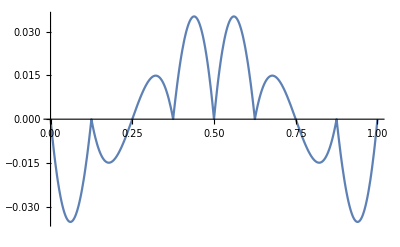

```mathematica
Plot3D[{test2D[x,y]-Reconstruct2D[hierarchicalCoefficients2D[test2D,3,3]]},{x,0,1},{y,0,1}]
Plot[{test[x]-Reconstruct[hierarchicalCoefficients[test,3]]},{x,0,1}]
```

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,2^-row i,2^(-(diag-row+1)) j,row,(diag-row+1)],{i,1,2^row-1,2},{j,1,2^(diag-row+1)-1,2}],{row,1,diag}],{diag,1,n}]
sparseReconstruct[coefficients_]:=Sum[Sum[Sum[coefficients[[diag,row,i,j]] ϕ[2^row(x-2^-row(2i-1))] ϕ[2^(diag-row+1)(y-2^(-(diag-row+1))(2j-1))],{i,1,Length[coefficients[[diag,row]]]},{j,1,Length[coefficients[[diag,row,i]]]}],{row,1,Length[coefficients[[diag]]]}],{diag,1,Length[coefficients]}]
```

```mathematica
N[sparseCoefficients2D[test2D,3]];
N[hierarchicalCoefficients2D[test2D,3,3]];
```

```mathematica
sparseReconstruct[N[sparseCoefficients2D[test2D,3]]];
Reconstruct2D[N[hierarchicalCoefficients2D[test2D,3,3]]];
```

```mathematica
Plot3D[sparseReconstruct[sparseCoefficients2D[test2D,4]],{x,0,1},{y,0,1}]
Plot3D[sparseReconstruct[sparseCoefficients2D[test2D,5]],{x,0,1},{y,0,1}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[test2D[x,y]-sparseReconstruct[sparseCoefficients2D[test2D,4]],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
sparseError=Table[Sqrt[NIntegrate[(test2D[x,y]-sparseReconstruct[sparseCoefficients2D[test2D,n]])^2,{x,0,1},{y,0,1},PrecisionGoal-> 4]],{n,1,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.0698782,0.0698782,0.0207485,0.00861161,0.00309476}

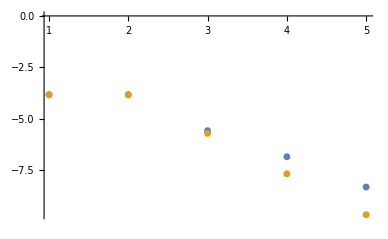

```mathematica
ListPlot[{
Table[{n,sparseError[[n]]//Log2},{n,1,5}],
Table[{n,error2D[[n]]//Log2},{n,1,5}]}
,PlotRange->All]
```